```mathematica
Ps=Table[{i,RandomInteger[5]},{i,1,15}]
```

{{1,5},{2,5},{3,2},{4,3},{5,1},{6,5},{7,4},{8,2},{9,4},{10,0},{11,0},{12,3},{13,4},{14,1},{15,0}}

```mathematica
curves=Table[With[{i=i},(1-3#+2#^2)Ps[[i-1]]+4#(1-#)Ps[[i]]+(-#+2#^2)Ps[[i+1]]&],{i,2,Length@Ps-1}];
```

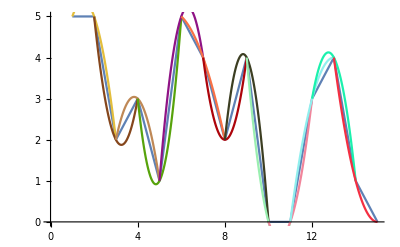

```mathematica
Show[
ListLinePlot[Ps],
ParametricPlot[Evaluate[#[t]&/@curves],{t,0,1},PlotStyle->RandomColor[Length@curves]]
]
```

```mathematica
innerCurves=Table[With[{i=k},Evaluate[(1-2#)curves[[i]][#+0.5]+2# curves[[i+1]][#]&]],{k,1,Length@curves-1}];
```

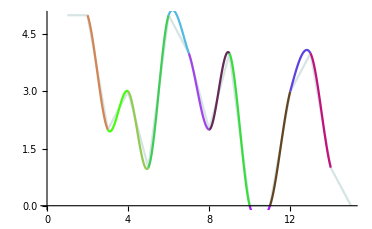

```mathematica
Show[
ListLinePlot[Ps,PlotStyle->Hue[0.5,0.5,0.5,0.21]],
ParametricPlot[Evaluate[#[t]&/@innerCurves],{t,0,0.5},PlotStyle->RandomColor[Length@innerCurves]]
]
```

```mathematica
curves2=Table[With[{i=i},(-4#^3+4#^2-#)Ps[[i-1]]+(12#^3-10#^2+1)Ps[[i]]+(-12#^3+8#^2+#)Ps[[i+1]]+(4#^3-2#^2)Ps[[i+2]]&],{i,2,Length@Ps-2}];
```

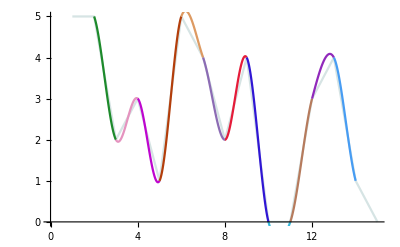

```mathematica
Show[
ListLinePlot[Ps,PlotStyle->Hue[0.5,0.5,0.5,0.21]],
ParametricPlot[Evaluate[#[t]&/@curves2],{t,0,0.5},PlotStyle->RandomColor[Length@innerCurves]]
]
```

```mathematica
img=Import["E:\\assignments\\2023-04-26-Parabola\\version 2\\img\\daijin.jpg"];
Show[edges=EdgeDetect[img],ImageSize->Medium];
```

```mathematica
img=Import[NotebookDirectory[]<>"..\\resources\\img1.jpg"]
Show[edges=EdgeDetect[img],ImageSize->Medium]
```

-Graphics-

-Graphics-

```mathematica
mask=Binarize[img,0.9]//ColorNegate
```

-Graphics-

```mathematica
Export["mask1.png",mask]
```

mask1.png

```mathematica
(* https://mathematica.stackexchange.com/questions/233092/how-can-i-extract-the-edge-points-from-an-image *)
```

```mathematica
data=Join@@Values[ComponentMeasurements[Binarize@edges,"Contours",#Count>40&]]/. Line[x_]:>x;
Row[ListPlot[data,Joined->#,ImageSize->400]&/@{False,True},Spacer[10]]
```

-Graphics--Graphics-

```mathematica
data=Select[data[[All,1;;;;8]],Length[#]>3&];
```

```mathematica
$stream=OpenWrite["file.txt",BinaryFormat->True]
```

OutputStream[…]

```mathematica
For[i=1,i<=Length[data],i++,
WriteString[$stream,"#,"<>ToString[Length[data]]<>",-1\n"];
Export[$stream,{"p"}~Join~#&/@data[[i]],"Table","FieldSeparators"->",","TextDelimiters"->""];
WriteString[$stream,"\n"];
]
Close[$stream]
```

file.txt

```mathematica
curves=Table[Table[With[{i=i,k=k},(-4#^3+4#^2-#)data[[k,i-1]]+(12#^3-10#^2+1)data[[k,i]]+(-12#^3+8#^2+#)data[[k,i+1]]+(4#^3-2#^2)data[[k,i+2]]&],{i,2,Length@data[[k]]-2}],{k,1,Length@data}]//Flatten;
```

```mathematica
Length@curves
Length@data
```

3093

136

```mathematica
Show[
ParametricPlot[Evaluate[#[t]&/@curves[[1;;1000]]],{t,0,0.5},PlotStyle->Gray]
]
```

$Aborted